```mathematica
(*Import the data*)
```

```mathematica
data=Import["./Downloads/transposed_data_subset_species_level.tsv","tsv"];
```

```mathematica
(*for h4015*)
```

```mathematica
h4015={};
Do[AppendTo[h4015,Drop[Transpose[data][[n]],{2,23}]],{n,1,Length[Transpose[data]]}]
```

```mathematica
h4015[[1]]
```

{,HSM5MD5X_P,HSM5MD62,HSM5MD6Y,HSM5MD71,HSM5MD73,HSM5MD75,HSM6XRS4,HSM6XRS6,HSM6XRS8,HSM6XRSE,HSM7CYZ5,HSM7CYZ7,HSM7CYZ9,HSM7CYZB,HSM7CYZD,HSM7CYZF,HSM7J4QB,HSM7J4QD,HSM7J4QF,HSM7J4QH,HSM7J4QJ,HSM7J4QL}

```mathematica
(*Transpose data to select the top 15 species*)
```

```mathematica
trans=h4015;
total={};
Do[AppendTo[total,Total[Drop[trans[[n]],1]]],{n,2,Length[trans]}]
```

```mathematica
topx=15;
```

```mathematica
top15={};
Do[AppendTo[top15,trans[[Flatten[Position[total,TakeLargest[total,topx][[n]]]]+1]]],{n,1,topx}]
```

```mathematica
(*put all the information for plotting in one*)
```

```mathematica
all={};
AppendTo[all,Drop[Transpose[data][[1]],{2,23}]];Do[AppendTo[all,Flatten[top15[[n]]]],{n,1,topx}]
```

```mathematica
Length[top15]
```

15

```mathematica
(*add "other" for all the samples*)
```

```mathematica
Length[all]
```

16

```mathematica
Length[all[[3]]]
```

23

```mathematica
other={};
Do[AppendTo[other,1-Total[Drop[Transpose[all][[n]],1]]],{n,2,23}]
```

```mathematica
all = Insert[all,Flatten[{"other",other}],2];
```

```mathematica
Length[all]
```

17

```mathematica
(*create the genus name for labeling*)
names={};
Do[AppendTo[names,StringSplit[Transpose[all][[1]],"|"][[n,7]]],{n,3,Length[Transpose[all][[1]]]}]
```

```mathematica
names
```

{s__Faecalibacterium_prausnitzii,s__Bacteroides_fragilis,s__Sutterella_wadsworthensis,s__Eubacterium_rectale,s__Roseburia_intestinalis,s__Bacteroides_vulgatus,s__Peptostreptococcaceae_noname_unclassified,s__Bacteroides_thetaiotaomicron,s__Bacteroides_caccae,s__Haemophilus_parainfluenzae,s__Escherichia_coli,s__Veillonella_unclassified,s__Bacteroides_ovatus,s__Bifidobacterium_longum,s__Enterobacter_cloacae}

```mathematica
namesn={};
Do[AppendTo[namesn,Capitalize[StringSplit[names,"__"][[n,2]]]],{n,1,Length[names]}]
```

```mathematica
namesn
```

{Faecalibacterium_prausnitzii,Bacteroides_fragilis,Sutterella_wadsworthensis,Eubacterium_rectale,Roseburia_intestinalis,Bacteroides_vulgatus,Peptostreptococcaceae_noname_unclassified,Bacteroides_thetaiotaomicron,Bacteroides_caccae,Haemophilus_parainfluenzae,Escherichia_coli,Veillonella_unclassified,Bacteroides_ovatus,Bifidobacterium_longum,Enterobacter_cloacae}

```mathematica
namesn1=Insert[namesn,"other",1]
```

{other,Faecalibacterium_prausnitzii,Bacteroides_fragilis,Sutterella_wadsworthensis,Eubacterium_rectale,Roseburia_intestinalis,Bacteroides_vulgatus,Peptostreptococcaceae_noname_unclassified,Bacteroides_thetaiotaomicron,Bacteroides_caccae,Haemophilus_parainfluenzae,Escherichia_coli,Veillonella_unclassified,Bacteroides_ovatus,Bifidobacterium_longum,Enterobacter_cloacae}

```mathematica
Length[namesn1]
```

16

```mathematica
(*Plotting*)
```

```mathematica
data=Drop[Transpose[Drop[all,1]],1];
```

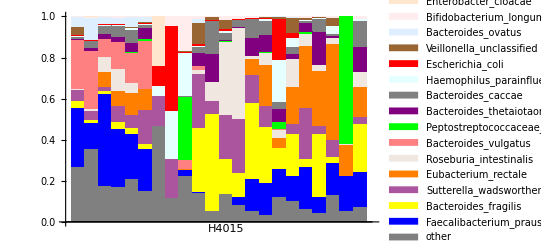

```mathematica
BarChart[data,ChartLabels->{{,,,,,,,,,,,"H4015",,,,,,,,,},None},
ChartLayout -> "Stacked",ChartStyle -> { Gray,Blue,Yellow,Blend[{Purple,LightYellow},1/3],Orange, LightBrown,Pink,Green, Purple, Gray,LightCyan,Red,Brown, LightBlue, LightPink,LightOrange},ChartLegends->namesn1,BaseStyle->{FontWeight->"Bold",FontSize->12},AxesStyle->Directive[Black,12]]
```